# Arm state visualization

## Import

```mathematica
(*ClearAll["Global`*"]
Clear["Global`*"]*)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_16__19_07_28"; (* range: 40 deg *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_17__09_34_18";(* range: 50 deg *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_17__13_32_26";(* range: 60 deg 2*)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_17__12_20_59";(* range: 60 deg *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_17__09_34_18";(* range: 50 deg *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_17__16_12_34";(* range: 50 deg *)


figExpPath="~thomasbuhrmann/Dropbox/eSMCs/publications/InteractionTorques/Figures/Mathematica/";

SetDirectory[dirName];
all=Import["State.txt", "Table"];
varNames=all[[1]]
data = all[[2;;-1]];
numVars=Dimensions[varNames];
numData=Length[data]

fitXml = Import["GA_Progress.xml"];
fitness=Cases[fitXml,XMLElement["Generation",{_,"BestFitness"->fit_,_},___]->fit,Infinity];
fitness=ToExpression[fitness];
font="Arial";
```

{NeuralExtInput0,NeuralExtInput1,NeuralExtInput2,NeuralExtInput3,NeuralExtInput4,NeuralExtInput5,NeuralExtInput6,NeuralExtInput7,NeuralOutput0,NeuralOutput1,NeuralOutput2,NeuralOutput3,NeuralOutput4,NeuralOutput5,NeuralOutput6,NeuralOutput7,NeuralState0,NeuralState1,NeuralState2,NeuralState3,NeuralState4,NeuralState5,NeuralState6,NeuralState7,accelerationElbow,accelerationShoulder,angleElbow,angleShoulder,coriolisElbow,coriolisShoulder,dampingElbow,dampingShoulder,elbX,elbY,gravityElbow,gravityShoulder,inertiaElbow,inertiaShoulder,interactionElbow,interactionShoulder,lineX1,lineX2,lineY1,lineY2,torqueElbow,torqueShoulder,velocityElbow,velocityShoulder,x,y}

28001

## Fitness

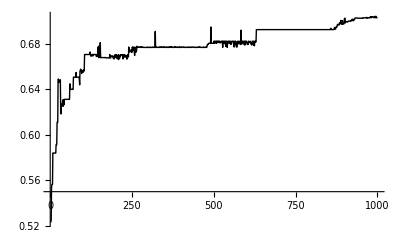

0.703751

```mathematica
fitP =ListLinePlot[fitness[[1;;Length[fitness]]],PlotStyle->Black,PlotRange->All,ImageSize->400]
maxFit = Max[fitness]
```

## Config

```mathematica
plotOptions = {PlotJoined->True, PlotRange->All};

dt =1/200;
T=14.0;
skip=7.0;
numTrials = Round[numData/(T/dt)]

SetTrial[trial_]:=Module[{},
t0=1+(trial*T+skip)/dt;
tn= t0+((T-skip)/dt)-1;
time=Range[tn-t0]*dt;
];

NtoI[name_]:=Position[varNames, name][[1,1]];

NtoD[name_]:=Table[data[[i,NtoI[name]]],{i,t0,tn}];

TimePlot[name_, options_, Scale_:1] := Module[{},
ListLinePlot[Transpose[{time,Scale*NtoD[name]}], Join[options,plotOptions]]
];

XYPlot[tr_,name1_,name2_, options_] :=Module[{},
SetTrial[tr];
 ListLinePlot[Transpose[{NtoD[name1],NtoD[name2]}], Join[options,plotOptions]]
];

PlotEnvLine[t_,options_]:=Module[{x1i,x2i,y1i,y2i,x1,x2,y1,y2},
SetTrial[t];
x1i=NtoI["lineX1"];
x2i=NtoI["lineX2"];
y1i=NtoI["lineY1"];
y2i=NtoI["lineY2"];
x1 = data[[t0,x1i]];
x2 = data[[t0,x2i]];
y1 = data[[t0,y1i]];
y2 = data[[t0,y2i]];
ListLinePlot[{{x1,y1},{x2,y2}}, Join[options,plotOptions]]
];


SetTrial[0];
```

10

## Figures

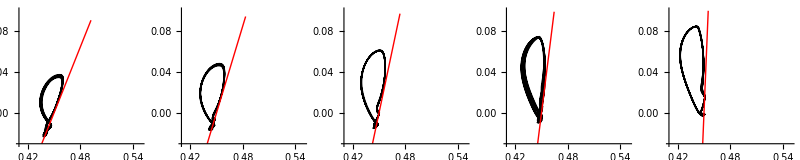

```mathematica
(*d=NtoD["x"]*)
range ={{0.41,0.55},{-0.03,0.1}};
origin={range[[1,1]],range[[2,1]]};
PlotLineTraj[t_,options_:{}]:=Module[{p1,p2},
p1=XYPlot[t,"x","y",Join[options,{PlotRange->range,PlotStyle->{Black},AxesOrigin->origin}]];
p2= PlotEnvLine[t,Join[options,{PlotRange->range,PlotStyle->{Red}}]];
Show[p1,p2]
];

GraphicsRow[Table[PlotLineTraj[i,{AspectRatio->Automatic, PlotRange->range}],{i,0,4}],ImageSize->800]
```

Joint angle phase space

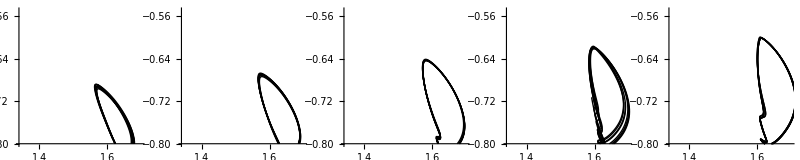

Sensor-shoulder phase space

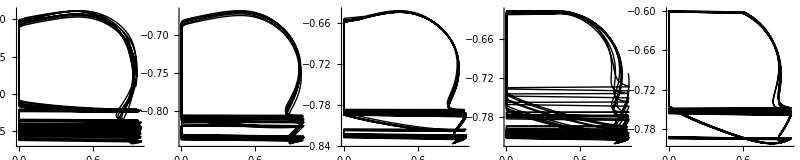

Sensor-elbow phase space

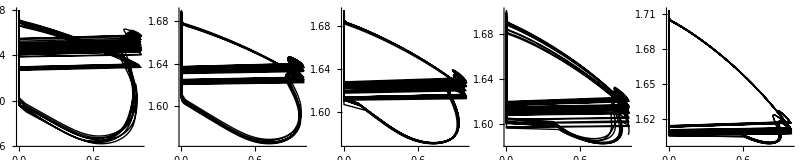

```mathematica
range = {{1.34,1.7},{-0.8,-0.55}};
origin={range[[1,1]],range[[2,1]]};
Print["Joint angle phase space"]
GraphicsRow[Table[XYPlot[i,"angleElbow","angleShoulder",{AspectRatio->1,PlotRange->range,PlotStyle->Black,AxesOrigin->origin}],{i,0,4}],ImageSize->800]

range = {{-0.1,1.1},{-0.8,-0.55}};
origin={range[[1,1]],range[[2,1]]};
Print["Sensor-shoulder phase space"]
GraphicsRow[Table[XYPlot[i,"NeuralExtInput0","angleShoulder",{AspectRatio->1,PlotStyle->Black,AxesOrigin->origin}],{i,0,4}],ImageSize->800]

range = {{-0.1,1.1},{1.34,1.7}};
origin={range[[1,1]],range[[2,1]]};
Print["Sensor-elbow phase space"]
GraphicsRow[Table[XYPlot[i,"NeuralState0","angleElbow",{AspectRatio->1,PlotStyle->Black,AxesOrigin->origin}],{i,0,4}],ImageSize->800]
```

```mathematica
121
```

121